```mathematica
choralesString=Import[FileNameJoin[{NotebookDirectory[],"Bach Dataset","chorales.lisp"}],"Text"];

choraleStrings=Select[StringSplit[choralesString,"\n"],StringLength[#]>0&];

makeNotes[chorale_]:=ToExpression/@StringCases[chorale,"((st "~~st:DigitCharacter..~~") (pitch "~~pitch:DigitCharacter..~~") (dur "~~dur:DigitCharacter..~~") (keysig "~~(DigitCharacter|"-")..~~") (timesig "~~DigitCharacter..~~") (fermata "~~ferm:DigitCharacter..~~"))"->{st,pitch,dur,ferm}]

makeSound[notes_]:=Sound[SoundNote[#[[2]]-60,{#[[1]]/8,#[[1]]/8+#[[3]]/8}]&/@notes]

makeNoteSequence[notes_]:=Module[{rests,noteList},
noteList=Join[{{0,0,0,0}},notes];
rests=#[[1]]-Drop[#[[3]],-1]&@MapAt[Differences,Transpose[noteList],1];
Cases[Riffle[noteList[[All,2;;]],{0,#,0}&/@rests],Except[{0,0,0}]]
]

sixteenthTime[sixteenths_,tempoBPM_]:= sixteenths 60/tempoBPM/4

makeSoundNotesFromNoteSequence[noteSequence_,tempoBPM_]:=noteSequence/.{{0,len_,ferm_}->SoundNote[None,sixteenthTime[len,tempoBPM],"Organ"],{note_,len_,ferm_}->SoundNote[note-60,sixteenthTime[len,tempoBPM],"Organ"]}

makeTokenStringFromNoteSequence[noteSequence_]:=StringRiffle[noteSequence/.{{0,len_,ferm_}:>"REST_"~~ToString[len],{note_,len_,ferm_}:>"NOTE_"~~ToString[note]~~"_"~~ToString[len]}," "]<>" END"

makeNoteSequenceFromTokenString[tokens_String]:=StringCases[tokens,{
"NOTE_"~~note:DigitCharacter..~~"_"~~length:DigitCharacter..:>{ToExpression[note],ToExpression[length],0},
"REST_"~~length:DigitCharacter..:>{0,ToExpression[length],0},
"END"->{0,16,0}}]
```

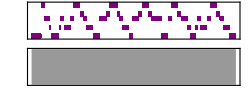
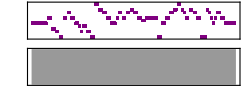
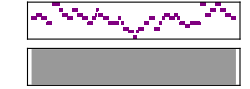
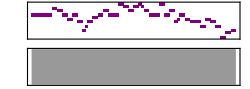
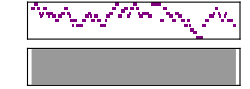
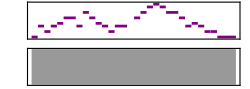
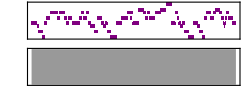
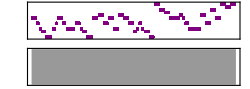
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
makeSound[makeNotes[#]]&/@choraleStrings
```

#### Make the note file with all the chorale melodies

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"bach_charale_maelodies_tokens.txt"}],
StringRiffle[makeStringFromNoteSequence/@makeNoteSequence/@makeNotes/@choraleStrings,"\n"]]
```

/Users/peter.sjogren/Google Drive/Mathematica/Nozzles/bach/bach_charale_maelodies_tokens.txt

#### Make note sequence from note token string

```mathematica
tokens="NOTE_7_14 NOTE_74_4 NOTE_69_4 NOTE_65_4 NOTE_62_8 NOTE_73_4 NOTE_74_4 NOTE_69_4 NOTE_77_4 NOTE_60_4 NOTE_72_4 NOTE_62_1 NOTE_61_4 NDTE_78_4 NOTE_69_4 NOTE_61_4 NOTE_74_4 NOTE_76_4 NOTE_72_4 NOTE_75_4 NOTE_64_4 NOOE_69_4 NNTE_7__4 NOTE_79_4 OOTE_74_4 NOTE_69_4 NOTE_68_4 NOTE_71_4 NOTE_70_4 NOTE_67_2 NOTE_73_2 NOTE_78_2 TNTE_7_8 NOTE_7S_4 NOTE_72_4 NOTE_77_4 OTE_64_4 NOTE_74_2 NOTE_67_4 NOTE_71_4 NOTE_74_4 NOTE_77_4 NOTE_75_8 NOTE_73_4 NOTE_72_2 NOTE_61_4 NNTE_66_4 NOTE_62_4 NOTE_74_4 OOTE_71_4 NNTE_76_4 NOTE_61_4 NOTE_77_8 NOTE_71_4 NOTE_72_8NNOT\n_70_2 NOTE_69_4 NOTE_67_8 NOTE_74_4 NOTE_71_4 NOTE_79_4 NOTE_73_2 NOTE_67_8 NOTE_67_4 OOTE__4_4 OOTE_76_4 NOTS_67_8 NOTE_62_4 NOTE_63_4 NOTE_72_4 NOTE_61_4 NOTE_61_4 NOTE_71_4 NOTE_74_4 NOTE_67_4 NOTE_66_2 NOTE_67_4 NOTE_69_4 NOTE_78_4 NOTE_78_4 NOTE_69_4 NOTE_69_4 NOTT_71_4 NOTE_62_4 NOTE_79_4 NOTE_74_4 NOTE_69_4 NOTE_69_2 NOTE_65_2 NOTE_67_4 OOTE_66_4 NOTE_73_4 NOTE_6S_4 2NOTE_69_6 NOTE_78_2 NOTE_7__4 NSE_69_4 NOTE_67_2 NOTE_78_4 NOTE_74_2 NOTE_62";
```

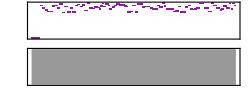

```mathematica
generated=Sound[makeSoundNotesFromNoteSequence[ makeNoteSequenceFromTokenString[tokens],120]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"generated.mp3"}],generated]
```

/Users/peter.sjogren/Google Drive/Mathematica/Nozzles/bach/generated.mp3

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"generated.mid"}],generated]
```

/Users/peter.sjogren/Google Drive/Mathematica/Nozzles/bach/generated.mid